# Examples treated by Chris Trana

### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Test 2

Select a ruleset to investigate, given its reduced rank index, quinary code, or ruleset, giving it some convenient name:

```mathematica
rs02=FromReducedRankIndex[2]
```

<|Index→2,QCode→0,RuleSet→{A→,→A}|>

We generate the sessie and its causal network, again giving it a convenient name:

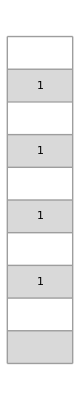
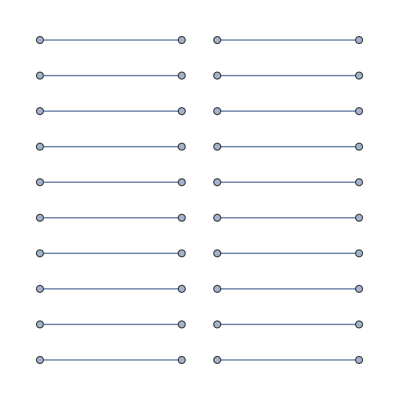
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss02=SSS[rs02[["RuleSet"]], "",40, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->10, HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss02[["Net"]]
```

{1→2,3→4,5→6,7→8,9→10,11→12,13→14,15→16,17→18,19→20,21→22,23→24,25→26,27→28,29→30,31→32,33→34,35→36,37→38,39→40}

```mathematica
nds02=ToNetDifferenceSets[sss02[["Net"]]]
```

{{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1}}

Try the reduction:

```mathematica
rsl02=ReduceSetList[nds02]
```

{€^19[{1},{}],{1}}

Look for a most compressed part.

Get an editable version of that last complete line:

```mathematica
rsl02[[1]]
```

€^19[{1},{}]

```mathematica
rsl02[[]]//InputForm
```

{IndexedConcatenate[{1}, {}, 19], {1}}

### Bottom Line:

RuleSet & IC form:

```mathematica
<|"Index"->2,"QCode"->"0","RuleSet"->{"A"->"",""->"A"}|>
```

```mathematica
rsl02[[1]]//InputForm
```

IndexedConcatenate[{1}, {}, 19]

```mathematica
IndexedConcatenate[{1}, {}, ∞]
```

€^∞[{1},{}]

### Chris Trana’s Summary

∪_(n=1)^∞{2n-1->2n}

{1→2,3→4,5→6,7→8,9→10,11→12,13→14,15→16,17→18,19→20,21→22,23→24,25→26,27→28,29→30,31→32,33→34,35→36,37→38,39→40}

How to get from here to there?

```mathematica
IndexedConcatenate[{1}, {}, {n,1,∞}]
```

€_(n⊨1)^∞[{1},{}]

We have to use the length of the subsequence in the IC: 2, and the 1:

∪_(n=1)^∞{2n-1->(2n-1)+1}

### Test 4

Select a ruleset to investigate, given its reduced rank index, quinary code, or ruleset, giving it some convenient name:

```mathematica
rs04=FromReducedRankIndex[4]
```

<|Index→4,QCode→2,RuleSet→{A→A}|>

We generate the sessie and its causal network, again giving it a convenient name:

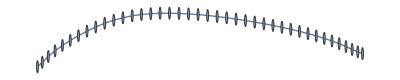
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
sss04=SSS[rs04[["RuleSet"]], "A",40, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->10, HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->400,SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss04[["Net"]]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20,20→21,21→22,22→23,23→24,24→25,25→26,26→27,27→28,28→29,29→30,30→31,31→32,32→33,33→34,34→35,35→36,36→37,37→38,38→39,39→40}

```mathematica
nds04=ToNetDifferenceSets[sss04[["Net"]]]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

Try the reduction:

```mathematica
rsl04=ReduceSetList[nds04]
```

{€^39[{1}]}

```mathematica
rsl04//InputForm
```

{IndexedConcatenate[{1}, 39]}

### Bottom Line:

RuleSet & IC form:

```mathematica
<|"Index"->4,"QCode"->"2","RuleSet"->{"A"->"A"}|>
```

```mathematica
rsl04//InputForm
```

```mathematica
{IndexedConcatenate[{1}, ∞]}
```

{€^∞[{1}]}

### Chris Trana’s Summary

∪_(n=1)^∞{n->n+1}

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20,20→21,21→22,22→23,23→24,24→25,25→26,26→27,27→28,28→29,29→30,30→31,31→32,32→33,33→34,34→35,35→36,36→37,37→38,38→39,39→40}

Again, using the length of the subsequence in the IC: 1, and the 1:

∪_(n=1)^∞{1n->1n+1}

### Test 888

Select a ruleset to investigate, given its reduced rank index, quinary code, or ruleset, giving it some convenient name:

```mathematica
rs888=FromReducedRankRuleSet[{"BA"->"AB","AB"->"AC","AC"->"CA","CA"->"BA"}]
```

<|Index→8883014856242566230,QCode→432342342344234424432443243,RuleSet→{BA→AB,AB→AC,AC→CA,CA→BA}|>

We generate the sessie and its causal network, again giving it a convenient name:

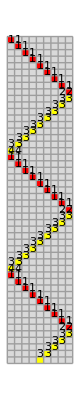


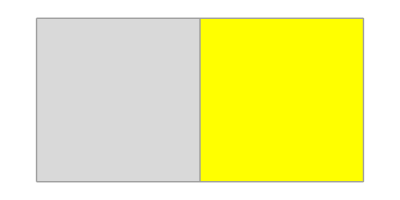
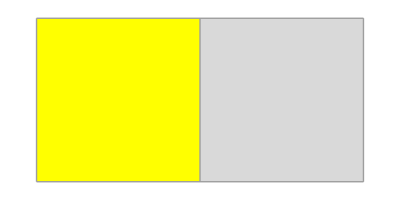
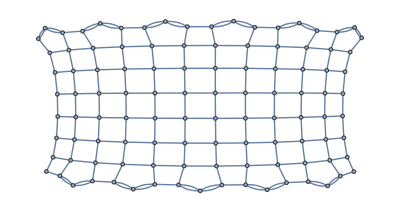
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss888=SSS[rs888[["RuleSet"]], "BAAAAAAAA",107, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->50, HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->400,SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss888[["Net"]]//Short
```

{1→2,2→3,3→4,4→5,5→6,«195»,104→105,92→106,105→106,91→107,106→107}

```mathematica
nds888=ToNetDifferenceSets[sss888[["Net"]]]
```

{{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1},{1},{1},{1},{1},{1},{1}}

Try the reduction:

```mathematica
rsl888=ReduceSetList[nds888]
```

{€^11[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]],€^7[{1}]}

```mathematica
rsl888[[1]]
```

€^11[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]]

```mathematica
InputForm[rsl888[[1]]]
```

IndexedConcatenate[{1, 16}, {1, 14}, {1, 12}, {1, 10}, {1, 8}, {1, 6}, 
 {1, 4}, IndexedConcatenate[{1, 1}, 2], 11]

### Bottom Line:

RuleSet & IC form:

<|Index→8883014856242566230,QCode→432342342344234424432443243,RuleSet→{BA→AB,AB→AC,AC→CA,CA→BA}|>

```mathematica
IndexedConcatenate[{1, 16}, {1, 14}, {1, 12}, {1, 10}, {1, 8}, {1, 6}, {1, 4}, 
 IndexedConcatenate[{1, 1}, 2], ∞]
```

€^∞[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]]

### Chris Trana’s Summary

∪_(n=0)^∞{...}:

This can be directly created from the slightly expanded version:

```mathematica
IndexedConcatenate[{1, 16}, {1, 14}, {1, 12}, {1, 10}, {1, 8}, {1, 6}, {1, 4}, 
{1, 1},{1, 1}, ∞]
```

€^∞[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1}]

∪_(n=0)^∞{(9n+1)->(9n+1)+1, (9n+1)->(9n+1)+16,
(9n+2)->(9n+2)+1, (9n+2)->(9n+2)+14,
(9n+3)->(9n+3)+1, (9n+3)->(9n+3)+12, 
(9n+4)->(9n+4)+1, (9n+4)->(9n+4)+10, 
(9n+5)->(9n+5)+1, (9n+5)->(9n+5)+8, 
(9n+6)->(9n+6)+1, (9n+6)->(9n+6)+6, 
(9n+7)->(9n+7)+1, (9n+7)->(9n+7)+4, 
(9n+8)->(9n+8)+1, (9n+8)->(9n+8)+1, 
(9n+9)->(9n+9)+1, (9n+9)->(9n+9)+1 
}

But can we get it from our most compressed version?  In fact, can it be compressed even further first?

```mathematica
IndexedConcatenate[{1, 16}, {1, 14}, {1, 12}, {1, 10}, {1, 8}, {1, 6}, {1, 4}, 
 IndexedConcatenate[{1, 1}, 2], ∞]
```

€^∞[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]]

```mathematica
IndexedConcatenate[
IndexedConcatenate[{1, 18-2k},{k,1,7}],
 IndexedConcatenate[{1, 1}, {k,1,2}],
{n,0,∞}]
```

€_(n⊨0)^∞[€_(k⊨1)^7[{1,18-2 k}],€_(k⊨1)^2[{1,1}]]

Or even:

```mathematica
IndexedConcatenate[
IndexedConcatenate[{1, 18-2k},{k,1,7}],
 IndexedConcatenate[{1, 1}, {k,8,9}],
{n,0,∞}]
```

€_(n⊨0)^∞[€_(k⊨1)^7[{1,18-2 k}],€_(k⊨8)^9[{1,1}]]

We’ll need to use the length of the subsequences in the IC: 7+2=9, and the numbers in our IC summary. It’s probably better to  name and show all indices, then we can explicitly use them in our constructed formula.

∪_(n=0)^∞(∪_(k=1)^7{(9n+k)->(9n+k)+1, (9n+k)->(9n+k)+18-2k} ∪
 ∪_(k=8)^9{(9n+k)->(9n+k)+1,(9n+k)->(9n+k)+1})

```mathematica
Flatten@Table[
Join[
Table[{(9n+k)->(9n+k)+1, (9n+k)->(9n+k)+18-2k} ,{k,1,7}],
Table[{(9n+k)->(9n+k)+1, (9n+k)->(9n+k)+1} ,{k,8,9}]
],
{n,0,3}]
```

{1→2,1→17,2→3,2→16,3→4,3→15,4→5,4→14,5→6,5→13,6→7,6→12,7→8,7→11,8→9,8→9,9→10,9→10,10→11,10→26,11→12,11→25,12→13,12→24,13→14,13→23,14→15,14→22,15→16,15→21,16→17,16→20,17→18,17→18,18→19,18→19,19→20,19→35,20→21,20→34,21→22,21→33,22→23,22→32,23→24,23→31,24→25,24→30,25→26,25→29,26→27,26→27,27→28,27→28,28→29,28→44,29→30,29→43,30→31,30→42,31→32,31→41,32→33,32→40,33→34,33→39,34→35,34→38,35→36,35→36,36→37,36→37}

```mathematica
Length[%33]
```

72

```mathematica
%33==Take[Sort[sss888[["Net"]]],72]
```

True

Hmmm, why didn’t ReduceSetList do the further reduction done by hand above?

```mathematica
$debug=True;
ReduceSetList[nds888]
$debug=False;
```

Entering ReduceSetList with: {{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},{1,1},{1,1},{1},{1},{1},{1},{1},{1},{1}}

exact repLen = 1: {{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],€^7[{1}]}

Entering improveReduction with: {{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],€^7[{1}]}

improved? : {{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],€^7[{1}]}

Entering ReduceSetList with: {{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}],€^7[{1}]}

exact repLen: 1

exact repLen: 2

exact repLen: 3

exact repLen: 4

exact repLen: 5

exact repLen: 6

exact repLen: 7

exact repLen: 8

Changed (in While): exact repLen = 8: {€^11[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]],€^7[{1}]}

Entering improveReduction with: {€^11[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]],€^7[{1}]}

improved? : {€^11[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]],€^7[{1}]}

Entering ReduceSetList with: {€^11[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]],€^7[{1}]}

exact repLen: 1

Exiting While[...replen...]

Treating Generic patterns

orig: {€^11[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]],€^7[{1}]}

generic: {€^0[{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},€^0[{1,1}]],€^0[{1}]}

generic repLen: 1, pos: {}

new varName: n$1

reduced? : {€^11[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]],€^7[{1}]}

{€^11[{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},€^2[{1,1}]],€^7[{1}]}

### Test2DCT

Select a ruleset to investigate, given its reduced rank index, quinary code, or ruleset, giving it some convenient name:

```mathematica
rs2DCT=FromReducedRankRuleSet[{"BA"->"AB","A"->"BAA"}]
```

<|Index→11643025,QCode→4323422433,RuleSet→{BA→AB,A→BAA}|>

We generate the sessie and its causal network, again giving it a convenient name:

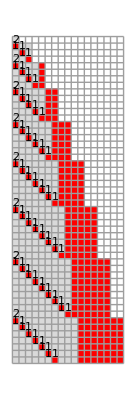
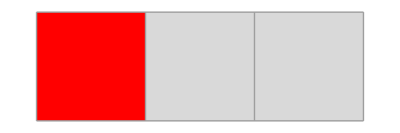
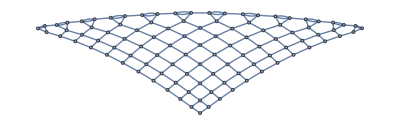
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss2DCT=SSS[rs2DCT[["RuleSet"]], "A",250, (* choose an appropriate initial state string, and # steps *)
(* options *)SSSMax->50, NetMax->102,HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->400,SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss2DCT[["Net"]]//Short[#,10]&
```

{1→2,1→2,2→3,1→3,2→4,4→5,4→5,5→6,4→6,6→7,3→7,5→8,8→9,8→9,9→10,8→10,10→11,6→11,11→12,7→12,9→13,13→14,13→14,14→15,13→15,15→16,10→16,16→17,11→17,17→18,12→18,14→19,19→20,19→20,20→21,19→21,21→22,15→22,22→23,16→23,23→24,17→24,24→25,18→25,20→26,26→27,26→27,27→28,«383»,205→226,226→227,206→227,227→228,207→228,209→229,229→230,229→230,230→231,229→231,231→232,210→232,232→233,211→233,233→234,212→234,234→235,213→235,235→236,214→236,236→237,215→237,237→238,216→238,238→239,217→239,239→240,218→240,240→241,219→241,241→242,220→242,242→243,221→243,243→244,222→244,244→245,223→245,245→246,224→246,246→247,225→247,247→248,226→248,248→249,227→249,249→250,228→250}

```mathematica
nds2DCT=ToNetDifferenceSets[sss2DCT[["Net"]]]
```

{{1,1,2},{1,2},{4},{1,1,2},{1,3},{1,5},{5},{1,1,2},{1,4},{1,6},{1,6},{6},{1,1,2},{1,5},{1,7},{1,7},{1,7},{7},{1,1,2},{1,6},{1,8},{1,8},{1,8},{1,8},{8},{1,1,2},{1,7},{1,9},{1,9},{1,9},{1,9},{1,9},{9},{1,1,2},{1,8},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10},{1,1,2},{1,9},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11},{1,1,2},{1,10},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12},{1,1,2},{1,11},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13},{1,1,2},{1,12},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14},{1,1,2},{1,13},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15},{1,1,2},{1,14},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16},{1,1,2},{1,15},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17},{1,1,2},{1,16},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18},{1,1,2},{1,17},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19},{1,1,2},{1,18},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20},{1,1,2},{1,19},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21},{1,1,2},{1,20},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22},{1,1,2},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

Try the reduction:

```mathematica
Position[nds2DCT,{1,1,2}]
```

{{1},{4},{8},{13},{19},{26},{34},{43},{53},{64},{76},{89},{103},{118},{134},{151},{169},{188},{208},{229}}

```mathematica
rsl2DCT=ReduceSetList[nds2DCT[[1;;228]]]
```

{{1,1,2},{1,2},{4},{1,1,2},€_(n$1⊨1)^2[{1,3+2 (-1+n$1)}],€_(n$2⊨1)^17[{4+n$2},{1,1,2},{1,3+n$2},€^(1+n$2)[{1,5+n$2}]],{22}}

```mathematica
rsl2DCT[[-2]]
```

€_(n$2⊨1)^17[{n$2+4},{1,1,2},{1,n$2+3},€^(n$2+1)[{1,n$2+5}]]

```mathematica
InputForm[rsl2DCT[[-2]]]/.n$2->n
```

```mathematica
{IndexedConcatenate[{4 + n}, {1, 1, 2}, {1, 3 + n}, 
 IndexedConcatenate[{1, 5 + n}, {k,1,1+n}], {n, -1, 0}]}//ExpandAll
```

{{3},{1,1,2},{1,2},{4},{1,1,2},{1,3},{1,5}}

```mathematica
{IndexedConcatenate[{1, 1, 2}, {1, 3 + n}, 
 IndexedConcatenate[{1, 5 + n}, {k,1,1+n}],
 {4 + n},
 {n, -1, 0}]}//ExpandAll
```

{{1,1,2},{1,2},{3},{1,1,2},{1,3},{1,5},{4}}

```mathematica
{IndexedConcatenate[{1, 1, 2}, {1, 3 + n}, 
 IndexedConcatenate[{1, 5 + n}, {k,1,1+n}],
 {5 + n},
 {n, -1, 5}]}
```

{€_(n⊨-1)^5[{1,1,2},{1,3+n},€_(k⊨1)^(1+n)[{1,5+n}],{5+n}]}

```mathematica
{IndexedConcatenate[{1, 1, 2}, {1, 1 + n}, 
 IndexedConcatenate[{1, 3 + n}, {k,1,n-1}],
 {3 + n},
 {n, 1, 19}]}
```

{€_(n⊨1)^19[{1,1,2},{1,1+n},€_(k⊨1)^(-1+n)[{1,3+n}],{3+n}]}

```mathematica
{IndexedConcatenate[{1, 1, 2}, {1, 1 + n}, 
 IndexedConcatenate[{1, 3 + n}, {k,1,n-1}],
 {3 + n},
 {n, 1, 19}]}//ExpandAll
```

{{1,1,2},{1,2},{4},{1,1,2},{1,3},{1,5},{5},{1,1,2},{1,4},{1,6},{1,6},{6},{1,1,2},{1,5},{1,7},{1,7},{1,7},{7},{1,1,2},{1,6},{1,8},{1,8},{1,8},{1,8},{8},{1,1,2},{1,7},{1,9},{1,9},{1,9},{1,9},{1,9},{9},{1,1,2},{1,8},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10},{1,1,2},{1,9},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11},{1,1,2},{1,10},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12},{1,1,2},{1,11},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13},{1,1,2},{1,12},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14},{1,1,2},{1,13},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15},{1,1,2},{1,14},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16},{1,1,2},{1,15},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17},{1,1,2},{1,16},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18},{1,1,2},{1,17},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19},{1,1,2},{1,18},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20},{1,1,2},{1,19},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21},{1,1,2},{1,20},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22}}

```mathematica
Length@%
```

228

```mathematica
nds2DCT[[1;;228]]==%71
```

True

### Bottom Line:

RuleSet & IC form:

```mathematica
{IndexedConcatenate[{1, 1, 2}, {1, 1 + n}, 
 IndexedConcatenate[{1, 3 + n}, {k,1,n-1}],
 {3 + n},
 {n, 1, ∞}]}
```

{€_(n⊨1)^∞[{1,1,2},{1,n+1},€_(k⊨1)^(n-1)[{1,n+3}],{n+3}]}

```mathematica
{IndexedConcatenate[{1, 1, 2}, {1, 2 + n}, 
 IndexedConcatenate[{1, 4 + n}, {k,1,n}],
 {4 + n},
 {n, 0, ∞}]}
```

{€_(n⊨0)^∞[{1,1,2},{1,n+2},€_(k⊨1)^n[{1,n+4}],{n+4}]}

```mathematica
{IndexedConcatenate[{1, 1, 2}, {1, 2 + n}, 
 IndexedConcatenate[{1, 4 + n}, {k,1,n}],
 {4 + n},
 {n, 0, 2}]} //ExpandAll
```

{{1,1,2},{1,2},{4},{1,1,2},{1,3},{1,5},{5},{1,1,2},{1,4},{1,6},{1,6},{6}}

```mathematica
Sum[k,{k,1,n-1}]//Expand
```

-n/2+n^2/2

Number of vertexes  in row n:

```mathematica
Table[(1/2)n^2+(1/2)n+3,{n,0,5}]
```

{3,4,6,9,13,18}

Number of vertexes  in row n and previous rows:

```mathematica
Accumulate@%
```

{3,7,13,22,35,53}

```mathematica
FindSequenceFunction[%,n]
```

1/6 (n^3+17 n)

```mathematica
FullSimplify@%
```

1/6 n (17+n^2)

```mathematica
Expand@%
```

(17 n)/6+n^3/6

```mathematica
(n^3+17 n)/6+2+n+1//Together
```

1/6 (18+23 n+n^3)

```mathematica
Simplify@%
```

1/6 (18+23 n+n^3)

```mathematica
FullSimplify@%
```

1/6 (n^3+23 n+18)

```mathematica
Table[%45,{n,0,4}]
```

{0,3,7,13,22}

### Chris Trana’s Summary

∪_(n=0)^∞{...}: